```mathematica
m=g=l=1 ;
sol =Solve[ m g l(1-Cos[θ])+ p^2/(2 m l^2) == H, p][[2]]
p=p/.sol
```

{p→√2 √(-1+H+Cos[θ])}

√2 √(-1+H+Cos[θ])

```mathematica
Jindf = Integrate[p,θ]  //Simplify
```

(2 √2 √(-1+H+Cos[θ]) EllipticE[θ/2,2/H])/(√((-1+H+Cos[θ])/H))

```mathematica
Jindf = (2 √2  EllipticE[θ/2,2/H])/(√(1/H))
```

(2 √2 EllipticE[θ/2,2/H])/(√(1/H))

```mathematica
extrema = Solve[p==0, θ][[2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{θ→ArcCos[1-H]}

```mathematica
J= 4((Jindf/.extrema) -(Jindf/.{θ->0}))/(2 π)
```

(4 √2 EllipticE[1/2 ArcCos[1-H],2/H])/(√(1/H) π)

```mathematica
dJdH = D[J,H]   //Simplify
```

(2 √2 √(1/H) EllipticF[1/2 ArcCos[1-H],2/H])/π

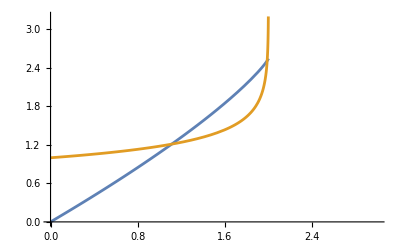

```mathematica
Plot[ {J, dJdH} , {H,0,3}]
```

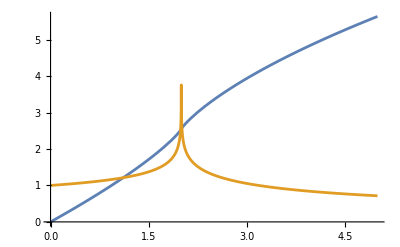

```mathematica
Plot[ { Re[J],Re[dJdH]} , {H,0,5}]
```

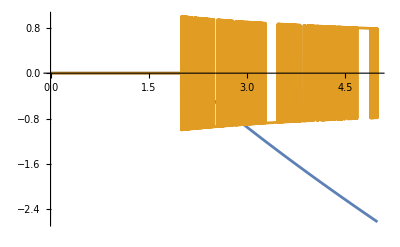

```mathematica
Plot[ { Im[J],Im[dJdH]} , {H,0,5}]
```

```mathematica
1000 //Pause
```

$Aborted

```mathematica
m=1;g=1;l=1;
H =m g l(1-Cos[θ])+ p^2/(2 m l^2) ;
J = (4 √2 EllipticE[1/2 ArcCos[1-H],2/H])/(√(1/H) π) ;

dJdθ = D[J,θ]   //Simplify  
dJdp =D[J,p]    //Simplify
dHdθ = D[H,θ]   //Simplify  
dHdp =D[H,p]   //Simplify
```

(4 √(1/(2+p^2-2 Cos[θ])) EllipticF[1/2 ArcCos[-p^2/2+Cos[θ]],4/(2+p^2-2 Cos[θ])] Sin[θ])/π

(4 p √(1/(2+p^2-2 Cos[θ])) EllipticF[1/2 ArcCos[-p^2/2+Cos[θ]],4/(2+p^2-2 Cos[θ])])/π

Sin[θ]

p

```mathematica
subsList1 = {p->ϵ 0, θ->π-ϵ};
subsList2 = {p->2-ϵ, θ->ϵ 0};
subsList = subsList1;
```

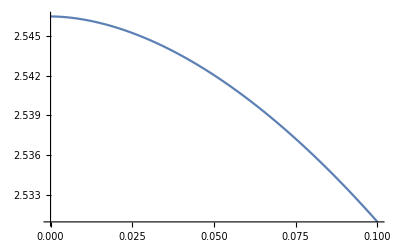

```mathematica
Plot[ (J/.subsList), {ϵ,0.0,0.1}, PlotRange->All]
```

1/π 4 √(1/(2+ϵ^2+2 Cos[ϵ])) EllipticF[1/2 ArcCos[-ϵ^2/2-Cos[ϵ]],4/(2+ϵ^2+2 Cos[ϵ])] Sin[ϵ]

Sin[ϵ]

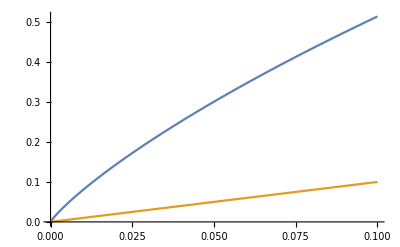

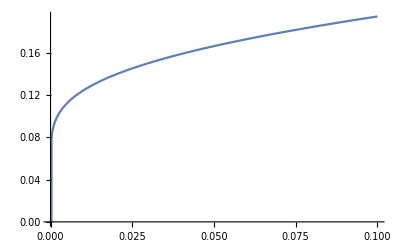

```mathematica
dJdθPlot =dJdθ       /.subsList1
dHdθPlot =dHdθ      /.subsList1
Plot[{Abs@dJdθPlot, Abs@dHdθPlot}, {ϵ,0.0,0.1}]
(*Plot[{Re@dJdθ, Re@dHdθ}, {ϵ,0,0.1}]
Plot[{Im@dJdθ, Im@dHdθ}, {ϵ,0,0.1}]*)
Plot[Abs@dHdθPlot/Abs@dJdθPlot, {ϵ,0,0.1}, PlotRange->All]
```

1/π 4 (2-ϵ) √(1/(2+(2-ϵ)^2-2 Cos[ϵ])) EllipticF[1/2 ArcCos[-1/2 (2-ϵ)^2+Cos[ϵ]],4/(2+(2-ϵ)^2-2 Cos[ϵ])]

2-ϵ

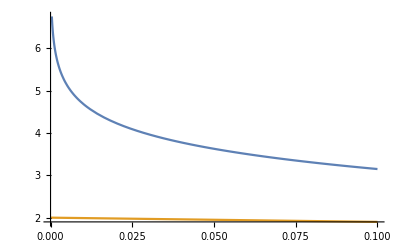

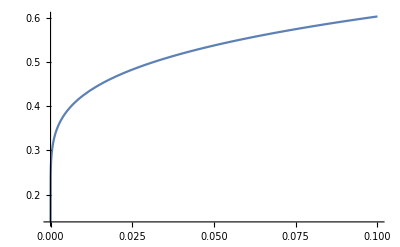

```mathematica
dJdpPlot =dJdp       /.subsList
dHdpPlot =dHdp       /.subsList
Plot[{Abs@dJdpPlot, Abs@dHdpPlot}, {ϵ,0.0,0.1}]
(*Plot[{Re@dJdp, Re@dHdp}, {ϵ,0,0.1}]
Plot[{Im@dJdp, Im@dHdp}, {ϵ,0,0.1}]*)
Plot[Abs@dHdpPlot/Abs@dJdpPlot, {ϵ,0,0.1}, PlotRange->All]
```

SURPRISING FINDINGS:
1. dJ blows up everywhere on the separatrix. At the critical point (CP), it blows up in a subtle manner: approach the CP from the separatrix side to see the blow up.
2. If C(x,y) has dC = 0, then  dV_c/(dx dy)^(1/2) ->0, where dx=dy and dV_c = differential volume in C space